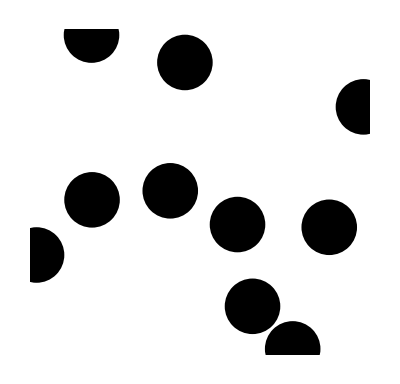

```mathematica
Graphics[{PointSize[.1],Point[{RandomReal[],RandomReal[]}]&/@Range[10]}]
```

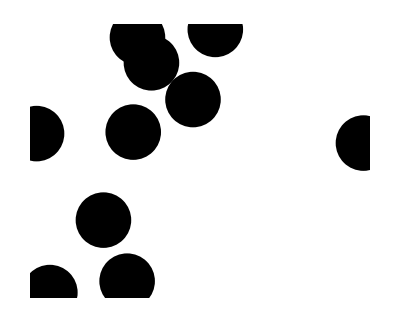

```mathematica
Graphics[{PointSize[.1],Point[{RandomVariate[NormalDistribution[0,.251]],RandomVariate[NormalDistribution[0,.251]]}]&/@Range[10]},PlotRange->1]
```

```mathematica
Dilation[Graphics[{PointSize[.051],Point[{RandomVariate[NormalDistribution[0,.251]],RandomVariate[NormalDistribution[0,.251]]}]&/@Range[200]},PlotRange->1],4]
```

-Graphics-

```mathematica
puntos=Point[{RandomVariate[NormalDistribution[0,.251]],RandomVariate[NormalDistribution[0,.251]]}]&/@Range[500];
```

```mathematica
Manipulate[Dilation[Graphics[{PointSize[.0251],puntos},PlotRange->1],DiskMatrix[k]],{{k,1},0,10}]
```

```mathematica
Manipulate[mode[Graphics[{Opacity[.3],PointSize[ps],puntos},PlotRange->1],DiskMatrix[k]],{{k,1},0,10},{{ps,.05},0,.2}]
```

```mathematica
RandomVariate[
```

```mathematica
puntos=Point[{RandomReal[],RandomReal[]}]&/@Range[1000];
```

```mathematica
{Slider[Dynamic[ds],{0,2}],Dynamic[ds],Slider[Dynamic[ps],{0,.13}],Dynamic[ps]}
```

{,,,}

```mathematica
Slider[Dynamic[mode],{{Dilation,Erosion}}]
```

```mathematica
mode=Dilation;
```

```mathematica
Dynamic[mode[Graphics[{PointSize[ps],puntos}],DiskMatrix[ds]]]
```

```mathematica
puntos2={Hue[RandomReal[]],Point[{RandomReal[],RandomReal[]}]}&/@Range[1000];
```

```mathematica
Dynamic[mode[Graphics[{PointSize[ps],puntos2}],DiskMatrix[ds]]]
```

```mathematica
Dynamic[mode[Graphics[{PointSize[ps],puntos2}],{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}]]
```

```mathematica
{Slider[Dynamic[ds],{0,2}],Dynamic[ds],Slider[Dynamic[ps],{0,.13}],Dynamic[ps]}
```

{,,,}

```mathematica
Slider[Dynamic[mode],{{Dilation,Erosion}}]
```

```mathematica
puntos3={Hue[Sqrt[(r+1)]+r2],Point[{r=.1 Mod[#,10],r2=RandomReal[]}]}&/@Range[1000];
```

```mathematica
Dynamic[mode[Graphics[{PointSize[ps],puntos3}],{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}]]
```

```mathematica
{Slider[Dynamic[ds],{0,20}],Dynamic[ds],Slider[Dynamic[ps],{0,.13}],Dynamic[ps]}
```

{,,,}

```mathematica
Slider[Dynamic[mode],{{Dilation,Erosion}}]
```

```mathematica
puntos4={Hue[.2r],Point[{r=Mod[#,7],r RandomVariate[NormalDistribution[]]}]}&/@Range[500];
```

```mathematica
Dynamic[mode[Graphics[{PointSize[ps],puntos4}],DiskMatrix[ds]]]
```

```mathematica
Clear[y]
```

```mathematica
?x
```

Global`x

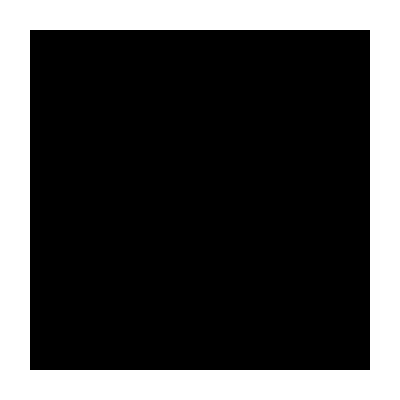

```mathematica
Graphics[Table[{PointSize[.1],Point[{x,y}]},{x,1,10},{y,1,10}]]
```

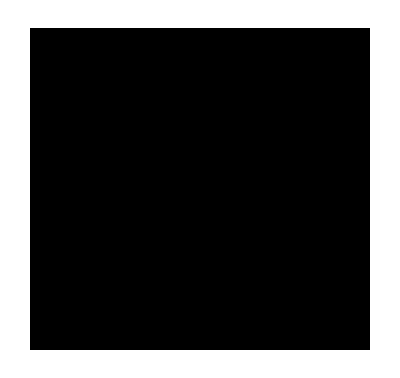

```mathematica
Graphics[Table[{PointSize[.1],Point[{x-.25(-1)^y,y}]},{x,1,10},{y,1,10}]]
```

```mathematica
n=5;Table[{If[i==(n+1)/2,1,0],If[j==(n+1)/2,1,0]},{i,1,n},{j,1,n}]
```

{{{0,0},{0,0},{0,1},{0,0},{0,0}},{{0,0},{0,0},{0,1},{0,0},{0,0}},{{1,0},{1,0},{1,1},{1,0},{1,0}},{{0,0},{0,0},{0,1},{0,0},{0,0}},{{0,0},{0,0},{0,1},{0,0},{0,0}}}

```mathematica
Table[{j,k},{j,1,10},{k,1,3+j}]
```

{{{1,1},{1,2},{1,3},{1,4}},{{2,1},{2,2},{2,3},{2,4},{2,5}},{{3,1},{3,2},{3,3},{3,4},{3,5},{3,6}},{{4,1},{4,2},{4,3},{4,4},{4,5},{4,6},{4,7}},{{5,1},{5,2},{5,3},{5,4},{5,5},{5,6},{5,7},{5,8}},{{6,1},{6,2},{6,3},{6,4},{6,5},{6,6},{6,7},{6,8},{6,9}},{{7,1},{7,2},{7,3},{7,4},{7,5},{7,6},{7,7},{7,8},{7,9},{7,10}},{{8,1},{8,2},{8,3},{8,4},{8,5},{8,6},{8,7},{8,8},{8,9},{8,10},{8,11}},{{9,1},{9,2},{9,3},{9,4},{9,5},{9,6},{9,7},{9,8},{9,9},{9,10},{9,11},{9,12}},{{10,1},{10,2},{10,3},{10,4},{10,5},{10,6},{10,7},{10,8},{10,9},{10,10},{10,11},{10,12},{10,13}}}

```mathematica
{Table[{j,k},{j,1,10},{k,1,3}]//MatrixForm,Table[{fila,columna},{fila,1,10},{columna,1,10-fila+10}]//MatrixForm}
```

{((1
1) | (1
2) | (1
3)
(2
1) | (2
2) | (2
3)
(3
1) | (3
2) | (3
3)
(4
1) | (4
2) | (4
3)
(5
1) | (5
2) | (5
3)
(6
1) | (6
2) | (6
3)
(7
1) | (7
2) | (7
3)
(8
1) | (8
2) | (8
3)
(9
1) | (9
2) | (9
3)
(10
1) | (10
2) | (10
3)),({{1,1},{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{1,8},{1,9},{1,10},{1,11},{1,12},{1,13},{1,14},{1,15},{1,16},{1,17},{1,18},{1,19}}
{{2,1},{2,2},{2,3},{2,4},{2,5},{2,6},{2,7},{2,8},{2,9},{2,10},{2,11},{2,12},{2,13},{2,14},{2,15},{2,16},{2,17},{2,18}}
{{3,1},{3,2},{3,3},{3,4},{3,5},{3,6},{3,7},{3,8},{3,9},{3,10},{3,11},{3,12},{3,13},{3,14},{3,15},{3,16},{3,17}}
{{4,1},{4,2},{4,3},{4,4},{4,5},{4,6},{4,7},{4,8},{4,9},{4,10},{4,11},{4,12},{4,13},{4,14},{4,15},{4,16}}
{{5,1},{5,2},{5,3},{5,4},{5,5},{5,6},{5,7},{5,8},{5,9},{5,10},{5,11},{5,12},{5,13},{5,14},{5,15}}
{{6,1},{6,2},{6,3},{6,4},{6,5},{6,6},{6,7},{6,8},{6,9},{6,10},{6,11},{6,12},{6,13},{6,14}}
{{7,1},{7,2},{7,3},{7,4},{7,5},{7,6},{7,7},{7,8},{7,9},{7,10},{7,11},{7,12},{7,13}}
{{8,1},{8,2},{8,3},{8,4},{8,5},{8,6},{8,7},{8,8},{8,9},{8,10},{8,11},{8,12}}
{{9,1},{9,2},{9,3},{9,4},{9,5},{9,6},{9,7},{9,8},{9,9},{9,10},{9,11}}
{{10,1},{10,2},{10,3},{10,4},{10,5},{10,6},{10,7},{10,8},{10,9},{10,10}})}

```mathematica
crossMatrix//Clear
```

```mathematica
crossMatrix[n_]:=Table[If[i==(n+1)/2|| j==(n+1)/2,1,0],{i,1,n},{j,1,n}];
```

```mathematica
crossMatrix[n_,grosor_]:=Table[If[Abs[i-(n+1)/2]<grosor|| Abs[j-(n+1)/2]<grosor,1,0],{i,1,n},{j,1,n}];
```

```mathematica
crossMatrix[9,3]//MatrixForm
```

(0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 0
0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 0
0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 0)

```mathematica
{Slider[Dynamic[ds],{1,101,2}],Dynamic[ds],Slider[Dynamic[grosor],{1,ds,1}],Dynamic[grosor],Slider[Dynamic[ps],{0,.225}],Dynamic[ps],Slider[Dynamic[factor],{0,1}],Dynamic[factor]}
```

{,,,,,,,}

```mathematica
Slider[Dynamic[mode],{{Dilation,Erosion}}]
```

```mathematica
crossMatrix[7]//MatrixForm
```

(0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0)

```mathematica
Table[Mod[y,2],{y,1,10}]
```

{1,0,1,0,1,0,1,0,1,0}

```mathematica
Dynamic[mode[Graphics[Table[{PointSize[ps],Point[{x+Mod[x,1+Mod[x,Abs[y]+1]],y}]},{y,-10,10},{x,-20,5}]],crossMatrix[ds,grosor]]]
```

```mathematica
Dynamic[mode[Graphics[Table[{PointSize[ps],Point[{x+Mod[x,1+Mod[x,Abs[y]+1]],y}]},{y,-10,10},{x,-20,5}]],crossMatrix[ds,grosor]]]
```

```mathematica
Dynamic[mode[Graphics[Table[{PointSize[ps],Point[{x+Mod[x,1+Mod[y,Abs[x]+1]],y}]},{y,-5,5},{x,-5,5}]],crossMatrix[ds,grosor]]]
```

```mathematica
Dynamic[mode[Graphics[Table[{PointSize[ps],Point[{x+.5Mod[y,3],y}]},{y,1,10},{x,1,10}]],crossMatrix[ds,grosor]]]
```

```mathematica
Dynamic[mode[Graphics[Table[{PointSize[ps],Point[{x+.5Mod[y,2],y}]},{y,1,10},{x,1,10}]],crossMatrix[ds,grosor]]]
```

```mathematica
Dynamic[mode[Graphics[Table[{PointSize[ps],Point[{x,y}]},{y,1,10},{x,1,10}]],crossMatrix[ds,grosor]]]
```

```mathematica
Dynamic[mode[Graphics[Table[{PointSize[ps],Point[{x-factor^y,y}]},{x,1,12},{y,-5,15+x}]],crossMatrix[ds]]]
```

```mathematica
Dynamic[mode[Graphics[Table[{PointSize[ps],Point[{x-factor^y,y}]},{x,1,10},{y,-2,15}]],crossMatrix[ds]]]
```

```mathematica
Dynamic[mode[Graphics[Table[{PointSize[ps],Point[{x-factor ^y(-1)^y,y}]},{x,1,10},{y,1,15}]],crossMatrix[ds]]]
```

```mathematica
Dynamic[mode[Graphics[Table[{PointSize[ps],Point[{x-factor x(-1)^y,y}]},{x,1,10},{y,1,10}]],crossMatrix[ds]]]
```

```mathematica
crossMatrix[n_]:=Table[If[i==(n+1)/2|| j==(n+1)/2,1,0],{i,1,n},{j,1,n}];Dynamic[mode[Graphics[Table[{PointSize[ps],Point[{x-factor(-1)^y,y}]},{x,1,10},{y,1,10}]],crossMatrix[ds]]]
```

Anterior exquisito las puntas delicadas con un cuerpo tan macizo... 
-Graphics-
/////////////

```mathematica
Dynamic[mode[Graphics[Table[{PointSize[ps],Point[{x-factor(-1)^y,y}]},{x,1,10},{y,1,10}]],IdentityMatrix[ds]]]
```

```mathematica
Dynamic[mode[Graphics[Table[{PointSize[ps],Point[{x-factor(-1)^y,y}]},{x,1,10},{y,1,10}]],ds]]
```

```mathematica
Dynamic[mode[Graphics[Table[{PointSize[ps],Point[{x-.25(-1)^y,y}]},{x,1,10},{y,1,10}]],IdentityMatrix[ds]]]
```

```mathematica
Dynamic[mode[Graphics[Table[{PointSize[ps],Point[{x,y}]},{x,1,10},{y,1,10}]],IdentityMatrix[ds]]]
```

Anterior se va viendo interesante.

```mathematica
Dynamic[mode[Graphics[Table[{PointSize[ps],Point[{x,y}]},{x,1,10},{y,1,10}]],ds]]
```

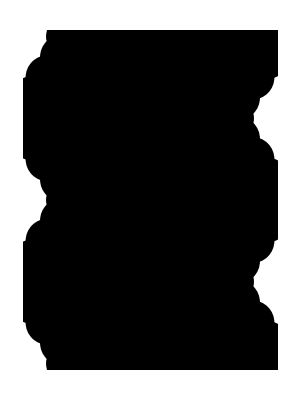

```mathematica
Graphics[Table[{PointSize[.08],Point[{x+Cos[2Pi(y)/8],y}]},{y,0,16},{x,0,10}]]
```

```mathematica
Reverse[ IdentityMatrix[3]]+IdentityMatrix[3]
```

{{1,0,1},{0,2,0},{1,0,1}}

```mathematica
Replace[Reverse[ IdentityMatrix[3]]+IdentityMatrix[3],2->1,2]
```

{{1,0,1},{0,1,0},{1,0,1}}

```mathematica
Replace[Reverse[ IdentityMatrix[3]]+IdentityMatrix[3],n_/;n>1->1,2]
```

{{1,0,1},{0,1,0},{1,0,1}}

```mathematica
matrixX[tam_]:=Replace[Reverse[ IdentityMatrix[tam]]+IdentityMatrix[tam],n_/;n>1->1,2]
```

```mathematica
{Slider[Dynamic[ds],{1,101,2}],Dynamic[ds],Slider[Dynamic[grosor],{1,ds,1}],Dynamic[grosor],Slider[Dynamic[ps],{0,.06125}],Dynamic[ps],Slider[Dynamic[factor],{0,1}],Dynamic[factor]}
```

{,,,,,,,}

```mathematica
Slider[Dynamic[mode],{{Dilation,Erosion}}]
```

```mathematica
Dynamic[mode[Graphics[Table[{PointSize[ps],Point[{x+1.2Cos[2Pi(y)/8],1.1y}]},{y,0,16},{x,-10,10}],ImageSize->1000],crossMatrix[ds,grosor]]]
```

```mathematica
Dynamic[mode[Graphics[Table[{PointSize[ps],Point[{x+1.2Cos[2Pi(y)/8],1.1y}]},{y,0,16},{x,-10,10}],ImageSize->1000],crossMatrix[ds,grosor]]]
```

```mathematica
Dynamic[mode[Graphics[Table[{PointSize[ps],Point[{x+Cos[2Pi(y)/8],1.1y}]},{y,0,16},{x,-10,10}],ImageSize->1000],crossMatrix[ds,grosor]]]
```

```mathematica
Dynamic[mode[Graphics[Table[{PointSize[ps],Point[{x+Cos[2Pi(y)/8],1.1y}]},{y,0,16},{x,-10,10}],ImageSize->1000],matrixX[ds]]]
```

```mathematica
Dynamic[mode[Graphics[Table[{PointSize[ps],Point[{x+Cos[2Pi(y)/8],1.2y}]},{y,0,16},{x,-10,10}],ImageSize->1000],matrixX[ds]]]
```

```mathematica
Dynamic[mode[Graphics[Table[{PointSize[ps],Point[{x+Cos[2Pi(y)/8],y}]},{y,0,16},{x,-10,10}],ImageSize->1000],matrixX[ds]]]
```

```mathematica
Dynamic[mode[Graphics[Table[{PointSize[ps],Point[{x+Cos[2Pi(y)/8],y}]},{y,0,16},{x,-10,10}],ImageSize->1000],ds]]
```